```mathematica
Clear[rb]
bin2[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
rb[n_,k_,a_]:=rb[n,k,a]=Sum[rb[Floor[n/j],k-1,a],{j,a,n}]
rb[n_,0,a_]:=UnitStep[n-1]
lrb[n_,a_]:=Sum[(-1)^(k+1)/k rb[n,k,a],{k,1,Log2@n}]
rbz[n_,z_,a_]:=Sum[bin2[z,k]rb[n,k,a],{k,0,Log2@n}]
lrz[n_,z_,a_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,a],{k,0,Log2@n}]
px[n_,z_,y_]:=If[n<y,1,Sum[bin2[z,k]px[n/y^k, z-k,y+1],{k,0,Log[y,n]}]]
px2[n_,k_,y_]:=Sum[(-1)^(k-j) bin2[k,j]px[n,j,y],{j,0,k}]
pxz[n_,z_,y_]:=Sum[bin2[z,k]Limit[lrz[n,j2,y],j2->k],{k,0,Log[y,n]}]
```

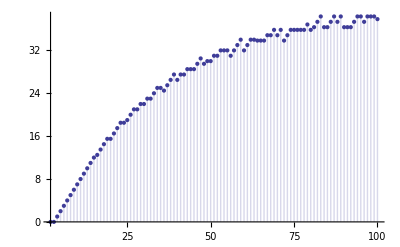

```mathematica
DiscretePlot[Limit[D[lrz[n,z,4],z],z->0],{n,2,100}]
```

```mathematica
DiscretePlot[D[px[n,z,4],z]/.z->0,{n,2,100}]
```

-Graphics-

```mathematica
Limit[lrz[100,z,3],z->3]
```

71

```mathematica
px2[100,3,3]
```

71

```mathematica
Expand@px[100,z,3]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
Expand@pxz[100,z,3]
```

1+(341 z)/12+(1391 z^2)/24+(139 z^3)/12+z^4/24

```mathematica
FullSimplify@Sum[Binomial[z,k]x^(0k)/k!,{k,0,Infinity}]
```

LaguerreL[z,-1]

```mathematica
N[D[LaguerreL[z,-(x^2)],z]/.z->0]/.x->100.
```

9.78756